```mathematica
data = {{0.1, 0.46648}, {0.156, 0.53563}, {0.212, 0.599255}, {0.268, 0.641507}, {0.324, 0.690263}, {0.38, 0.720694}, {0.436, 0.76207}, {0.492, 0.785497}, {0.548, 0.822419}, {0.604, 0.841076}, {0.66, 0.845012}, {0.716, 0.890145}, {0.772, 0.921945}, {0.828, 0.934329}, {0.884, 0.964532}, {0.94, 0.974688}, {0.966, 1.00366}, {1.052, 1.01196}, {1.108, 1.03995}, {1.164, 1.04666}, {1.22, 1.07387}, {1.276, 1.07921}, {1.322, 1.10578}, {1.388, 1.10991}, {1.444, 1.13594}};
Clear[a, b]
rules=FindFit[data, a+b*x+c*x^2, {a, b, c}, x]; y=a+b*x+c*x^2/.rules
```

0.426314+0.82612 x-0.241726 x^2

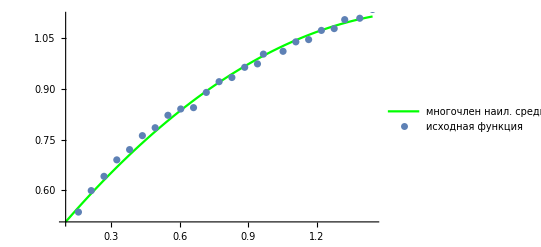

```mathematica
gr1:=Plot[y, {x, 0.1, 1.444}, PlotStyle->Green, PlotLegends->{"многочлен наил. cреднеквадр. 
 приближ. (2 степени)"}]

gr2:=ListPlot[data, PlotLegends->{"исходная функция"}]
Show[gr1, gr2]
```

```mathematica
check={};
For[i=1, i<Length[data], i=i+1,
newEl=(0.4263143982933064+0.8261202609680522 *data[[i, 1]]-0.2417264402931212* data[[i, 1]]^2-data[[i, 2]])^2;

check=Append[check, newEl]];
Total[check]
```

0.005005